## Lesson

Exact inputs give exact outputs:

```mathematica
1/2+1/3
```

5/6

Get numerical approximation:

```mathematica
N[1/2+1/3]
```

0.833333

Scientific notation:

```mathematica
2.7*^6
```

2.7×10^6

Generate random real numbers:

```mathematica
RandomReal[{20,30},5]
```

{20.7192,21.8756,29.4712,26.3573,26.3049}

Get the n^th prime number:

```mathematica
Prime[100]
```

541

Create a logarithmic plot:

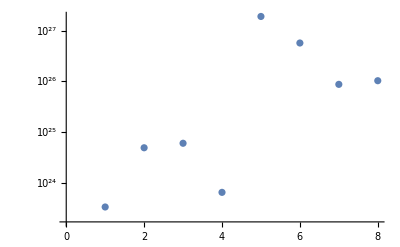

```mathematica
ListLogPlot[EntityClass["Planet",All]["Mass"]]
```

Absolute values:

```mathematica
{Abs[3],Abs[-3]}
```

{3,3}

Round to nearest whole:

```mathematica
{Round[3.2],Round[3.4],Round[3.6],Round[3.9]}
```

{3,3,4,4}

Modulo operator:

```mathematica
{Mod[50,60],Mod[55,60],Mod[60,60],Mod[65,60],Mod[70,60]}
```

{50,55,0,5,10}

## Questions

Q1. Find √2 to 500-digit precision.

```mathematica
N[√2,500]
```

1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276415727350138462309122970249248360558507372126441214970999358314132226659275055927557999505011527820605714701095599716059702745345968620147285174186408891986095523292304843087143214508397626036279952514079896872533965463318088296406206152583523950547457502877599617298355752203375318570113543746034084988471603868999706990048150305440277903164542478230684929369186215805784631115966687130130156185689872372

Q2. Generate 10 random real numbers between 0 and 1.

```mathematica
RandomReal[{0,1},10]
```

{0.435942,0.507843,0.782808,0.171793,0.678102,0.756226,0.842932,0.763584,0.642631,0.509344}

Q3. Make a plot of 200 points with random real x and y coordinates between 0 and 1.

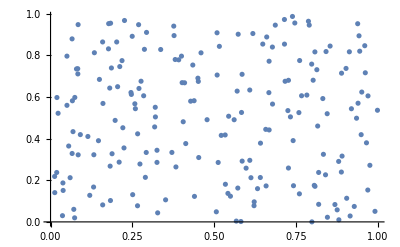

```mathematica
ListPlot[RandomReal[{0,1},{200,2}]]
```

Q4. Create a random walk using AnglePath and 1000 random real numbers between 0 and 2π.

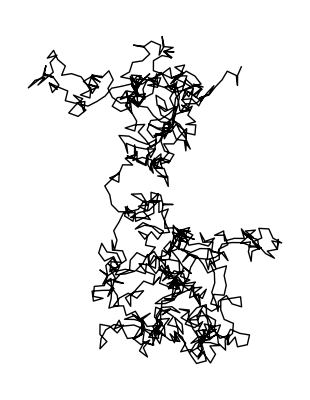

```mathematica
Graphics[Line[AnglePath[RandomReal[{0,2π},1000]]]]
```

Q5. Make a table of Mod[n^2, 10] for n from 0 to 30.

```mathematica
Mod[#^2,10]&/@Range[0,30]
```

{0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0}

Q6. Make a line plot of Mod[n^n, 10] for n from 1 to 100.

```mathematica
Mod[#^#,10]&/@Range[100]
```

{1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0}

Q7. Make a table of the first 10 powers of π, rounded to integers.

```mathematica
Round[π^#&/@Range[0,10]]
```

{1,3,10,31,97,306,961,3020,9489,29809,93648}

Q8. Make a graph by connecting n with Mod[n^2, 100] for n from 0 to 99.

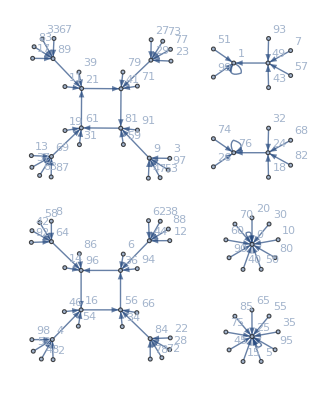

```mathematica
Graph[#->Mod[#^2,100]&/@Range[0,99],VertexLabels->Automatic]
```

Q9. Generate graphics of 50 circles with random real coordinates 0 to 10, random real radii from 0 to 2, and random colours.

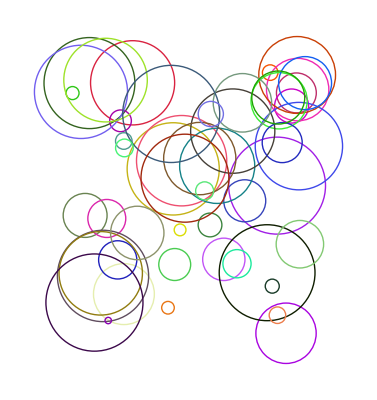

```mathematica
Graphics[Table[Style[Circle[RandomReal[{0,10},2],RandomReal[2]],RandomColor[]],50]]
```

Q10. Make a plot of the nth prime divided by n log(n), for n from 2 to 1000.

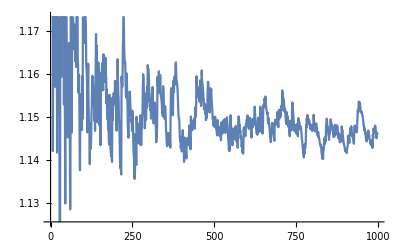

```mathematica
ListLinePlot[Prime[#]/(# Log[#])&/@Range[2,1000]]
```

Q11. Make a line plot of the differences between successive primes up to 100.

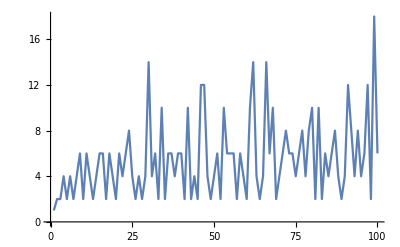

```mathematica
ListLinePlot[Prime[#+1]-Prime[#]&/@Range[100]]
```

Q12. Generate a sequence of 20 middle C notes with random durations between 0 and 0.5 seconds.

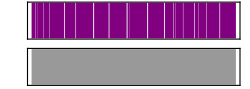

```mathematica
Sound[Table[SoundNote["C",RandomReal[0.5]],20]]
```

Q13. Make an array plot of Mod[i, j] for i and j up to 50.

```mathematica
ArrayPlot[Table[Mod[i,j],{i,50},{j,50}]]
```

-Graphics-

Q14. Make a list for n from 2 to 10 of array plots for x and y up to 50 of x^y mod n.

```mathematica
ArrayPlot[Table[Mod[x^y,#],{x,50},{y,50}]]&/@Range[2,10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Extended Questions

+Q1. Use Round to compute the fractional part of π to 50 digits.

```mathematica
N[π-Round[π],50]
```

0.14159265358979323846264338327950288419716939937511

+Q2. Find the sum of the first 1000 prime numbers.

```mathematica
Total[Prime[Range[1000]]]
```

3682913

+Q3. Make a list of the first 100 primes modulo 4.

```mathematica
Mod[Prime[Range[100]],4]
```

{2,3,1,3,3,1,1,3,3,1,3,1,1,3,3,1,3,1,3,3,1,3,3,1,1,1,3,3,1,1,3,3,1,3,1,3,1,3,3,1,3,1,3,1,1,3,3,3,3,1,1,3,1,3,1,3,1,3,1,1,3,1,3,3,1,1,3,1,3,1,1,3,3,1,3,3,1,1,1,1,3,1,3,1,3,3,1,1,1,3,3,3,3,3,3,3,1,1,3,1}

+Q4. Make a list of the first 10000 primes modulo 4, multiply them by 90° and create an angle path from them.

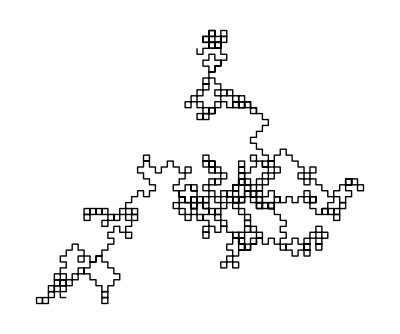

```mathematica
Graphics[Line[AnglePath[90° Mod[Prime[Range[1000]],4]]]]
```